# Introduction to Mathematica

## Acknowledgements

Parts of the material were edited by Tom Berlijn, tberlijn@science.uva.nl, for the course "Simuleren en Modelleren en Continue Wiskunde 2005" given by Alfons Hoekstra at the Faculty of Informatics of the University of Amsterdam.

Parts of the material in this section was taken from a number of sources, which are listed below

Mathematica 3.0, S. Wolfram.
Mathematica User's Guide to the X Front End, Wolfram Research.
Mathematical Modelling and Mathematica, J.E. Cruthirds and L.R. Hitt, Department of Mathematics and Statistics, University of South Alabama, material taken from the Web.
An introduction to Mathematica, N. Blachman, material taken from the Web.

## Introduction and demands for Report and grade calculation

This notebook will give an introduction to Mathematica. It gets you acquainted with a number of Mathematica. functions, and introduces the user interface. At the end of the notebook you will find a number of exercises. Present each exercise in the form of a full report and include the sections: "Introduction", "Methods", "Results" and "Discussion". Do NOT try to edit this notebook but use "Introduction_template.nb" to produce your  results. Upload your reports as one Mathematica notebook into BlackBoad.

## Grade Calculation

For each exercise a grade (1-10) is given. The mandatory exercises are weighted according to the following scheme.

exercise  | weight
1 | 1
2 | 2
3 | 2.5
4 | 2.5
5 | 2

The advanced exercise are optional. A maximum of 2 bonus points can be received. Bonus points  for an advanced exercise are given only if it is graded with a 6 or higher. The advanced exercises are weighted according to the following scheme.

exercise | weight
1 | 3
2 | 3
3 | 4

## Introducing Mathematica

## A.1 The Mathematica Front End and Kernel

### A.1.1 The Mathematica environment

Mathematica is a powerful desktop computer program capable of doing algebraic calculations, numerical approximations, computer graphics, and much more.

Mathematica consists of two parts, the Kernel, which is the computational engine, and the  Front End, which acts as the user interface to the Kernel. The Mathematica Kernel is essentially identical on all computer systems. The Front End may differ from one (operating) system to another. Mathematica  can be operated in many ways. The Kernel and Front End can both run at the same computer, or the Kernel may run on a powerful server with the Front End running on your local host. If a computation must be carried out, the Front End contacts the Kernel, e.g. through the network. Although the details of running Mathematica therefore differs from one place to another, the structure of Mathematica calculations is the same in all cases. You enter input, then the Mathematica Kernel processes it, and returns the result.

You will be using the Notebook Front End, which is available on many systems (Macintosh, Windows, Unix, etc.). Section 1.2 will discuss the Notebook Front End in more detail.

During the lab session you will be using Mathematica 3.0, which is the most recent version.  In our local WINS environment we have a campus wide license. During the lab work you will have both the Kernel and the Front End running on your local workstation.

### A.1.2 The Notebook Structure, Starting and Using the Kernel

#### The Notebook

Mathematica supports a special Notebook interface on most computers with a graphical user interface. In this section the structure of this Notebook is shortly explained and the Notebook Front End is introduced. Finally the use of the Kernel is explained, by starting the Kernel from the Notebook Front End and telling it that is should calculate 1+1 for us.

Currently you are reading a Mathematica Notebook. A notebook is a file containing text, input to the Kernel, and results of calculations, in textual or graphical form, all organised in a hierarchical way. A Notebook can be viewed as a folded piece of paper, which  can be unfolded at will. The folds in the file are called cells. Cells can enclose other cells, and may be opened or closed at will. The cell structure can be controlled by the vertical brackets on the right of this window. The hierarchical structure of a cell group is indicated by the layering of the cell brackets.

Mathematica groups cells automatically on the basis of the cell styles (unless you turn this off, using the Cell Grouping features in the Cell menu). For instance, a subsection is automatically grouped with text cells below the subsection cell, as drawn below. The text cell and Sub Section cell are both enclosed by a bracket, and one level up, again by a next bracket, indicating that both cells are grouped. As you see on the right of this Notebook, there are more than just two brackets, indicating higher levels of grouping of the cells.

Using the concept of cells containing certain types of information and grouping of cells, we can now take a look on folding up, or closing the cells. A closed cell is marked by an arrow at the bottom of the grouping bracket. By doubling clicking on such bracket, the closed group is opened, i.e. unfolded, and the contents is shown. Below, an example of such a closed cell is shown. Now open this cell and continue reading inside that cell.

#### a closed cell

This is an example of a closed cell (which off-course you just opened), containing text and some graphical output. Under the Style submenu in the Format menu you can asses the style of each specific cell. If you select the cell that you are currently reading, by clicking inside the cell or selecting the cell bracket (click on it once), and look into the Style submenu you will notice that it has the style Text. As you see, the Front End has a large number of predefined cell styles. If you start using the Notebook for the lab exercises you can experiment with the cell styles to create nicely formatted Notebooks, which can be handed over as lab journals. Also notice the StyleSheet submenu in the Format menu which has a large collection of predifined style sheets. Now find out about the cell styles of the three cells you see below. Also notice the special bracket symbols used for these cells.

```mathematica
Plot3D[Sin[x] Cos[y], {x,0, Pi},{y, 0, Pi}]
```

⁃SurfaceGraphics⁃

It will by now be clear that you can also close cell groups by double-clicking on the enclosing brackets. Note that if you do so, only the head cell of the closed group is visible. In the rest of this Notebook all sections and subsections are closed cells. To read them they should be opened. Closing all sections and subsection (you could do that now) results in an overview of the contents of the Notebook. You can use the Notebook to write your own (interactive, as will become clear later on) lab journals.

The contents of (text) cells can be edited as usual (i.e. inserting text, copying, cutting, pasting, etc., see the Edit menu). Complete (grouped) cells can also be copied and pasted in a Notebook. First, select the cell you want to copy by clicking its enclosing bracket, then choose Copy from the Edit menu, move the cursor to the place where you want to paste the cell. This can only be at places where the cursor changes in a horizontal bar, click (a horizontal line appears), and choose Paste from the Edit menu. As an exercise, try to copy this complete cell to another position in the Notebook.

#### More on Cell Properties

The properties of Cells control the display of material in your notebook, and also tell Mathematica how to treat particular cells when you perform an evaluation. Cell properties are controlled through the FormatType sub menus and the Cell Properties sub menu under the Cell menu. One of the most important properties of a cell is how it is formatted and if you can edit the cell. For instance, if you select this cell, and look under the Display As sub menu  you will notice that this cell is displayed as text. We will returrn to the FormatType of cells if we discuss Input and Output in Notebooks in more detail in section 1.4.

The cell below is graphical output from Mathematica. Such output is generated by the Kernel as postscript, and the Front End renders it. You can see the underlying postscript code by selecting the cell, and choosing Show Expression from the Format menu. Actually, just before the postscript code you see some Mathematica functions which are used by the Front End to display the total cell in a correct way. Actually, the overall notebook file is a plain Ascii file only containing such code. In this way the notebooks are fully portable among different computers. Choosing  Show Expression once more brings back the rendered picture.

A cell can either be Evaluatable or not (as is seen in the Cell Properties sub menu). An evaluatable cell is one that can be evaluated by the Mathematica Kernel, and usually contains mathematical expressions. Non-evaluatable cells contain material that you would ordinarily not want to evaluate, such as explanatory text (as in this cell), as well as Mathematica output. Non-evaluatable cells are marked with a horizontal tick mark near the top of their cell brackets, like the bracket of this cell.

Below is an example of an evaluatable cell, which is recognised by the plain bracket with the little triangle in the top. Checking the Style sub menu shows that it has the style Input. Also look at the cell properties. To evaluate the expression in the input cell (in this case 1+1) you select the cell, or click somewhere in the cell. Then, select from the Kernel menu Evaluation and Evaluate Cells, or faster, just press Shift-Return. As this is your first evaluation, the Mathematica Kernel is not running. So, after you pressed Shift-Return the Mathematica Kernel automatically starts up (this may take a while). For next evaluation the Kernel is already running. Next, the expression in the cell is sent to the Kernel, which evaluates it and sends the result back to the Front End. New cells below the input cells will be created automatically to place the results. Ok, just try to do this !

```mathematica
1+1
```

You should notice a few things. First, Mathematica assigns in sequence a number to each of the cells it evaluates, which is useful to address previous results in a longer calculation. Next, the output cell that was created automatically, and the input and output are automatically grouped. Notice again the bracket for the output cell. Now that you know about addition, try to enter, immediately below this cell, another expression (using the symbols *, /, or +) and evaluate it. Just move the cursor down, until it becomes a horizontal bar, click (now you see a line) and start typing your expression. Notice that by default the cell style is an evaluatable input cell. Notice also how Mathematica keeps track of the numbers of evaluations, how the output is organised, and play around with the difference between formatted and unformatted output.

Now you know how to use Mathematica as a calculator. In section 1.3 you will find some useful information about the on-line help facilities in Mathematica. In the following sections you will examine the mathematical and graphical capabilities, and also take a look at programming capabilities of Mathematica.

### A.1.3 Getting help in Mathematica

As will become clear Mathematica is a very large system, containing an enormous amount of functions (in the order of 1000). Furthermore, the Front End has many features. All information can of course be found in the user manuals and the Mathematica book (that will be present during lab hours). However, Mathematica has an extensive on-line help facility which will be of utmost importance to help you through this lab work. A full listing of the syntax and use of all functions and add-on packages is available. Extensive demos and tours through Mathematica are available, and the full Mathematica 3 book is available on-line. However, another very useful help facility is Why the Beep? If something goes wrong, Mathematica will beep. To find out what happened, choose the Why the Beep? command from the Help menu....

The Mathematica Help Browser will become an important companion for you. Choose Help in the Help menu. The help browser now pops up. You can get information from 6 different sources,

Built-in Functions
Getting Started/Demos
Add-ons
Other Information
The Mathematica Book
Master Index

By clicking the radio buttons you select the appropriate source. The Built-in Functions explains Mathematica functions. Add-ons gives access to all standard Mathematica Packages. The Getting Started/Demos gives a wealth of information beyond what is covered in this Lab Work and is helpful as background reading. Other Information fully explains all Menu Commands of the Front End, and gives some other very useful information in using the Front End efficiently. The Mathematica book is the on-line version of the 1400 pages Mathematica 3 book. All you need to know, and much more, is in there. To look up a specific function, start typing its name in the Go To box, or type the function name in a notebook cell, select the function name (e.g. by double-clicking on it), and select Find in Help from the Help menu. The Help Browser is a very useful tool when working with Mathematica.

As an exercise, you want to calculate the logarithm to base 10 of 2.5, but forget the function name in Mathematica . You know that the logarithm is an elementary mathematical function. Use the help browser to find the correct function name and calculate the result (which is 0.39794).

◼ See also the Mathematica book:  Section 1.3.8.

The blue thing is a hyperlink, just click it as you know from Web Browsers. They operate the same.

### A.1.4 Input and Output in Notebooks

#### A.1.4.1 Introduction

In previous versions of Mathematica all input was purely text based and in terms of functions. For instance, to calculate a variable x to the power 2 would be expressed as

```mathematica
Power[x,2]
```

or in shorthand, as

```mathematica
x^2
```

The output is shown below.

2
x

The format of both input cells above is InputForm as can be assessed from the Display As sub menu from the Cell menu. The output is in OutputForm, as can be seen in the Convert To sub menu from the Cell menu. Also, more complicated formula can be built up using this InputForm and OutputForm. An example is shown below.

```mathematica
(x^2 + y^6 - Sqrt[z])/(x^3 + z^2)
```

2    6
x  + y  - Sqrt[z]
-----------------
      3    2
     x  + z

Of course, for many mathematical functions a standard mathematical notation exists, which is probably easier to use. Furthermore, if you are working with formula manipulations and you want to print or publish the results you also want to have nicely formatted formulas, according to the accepted standards. In Mathematica 3 this is possible, and is the default way of entering mathematical formulas (although the fully text based approach in the InputForm and OutputForm can also still be used).

Below you now see the examples from above in nice mathematical notation.

```mathematica
x^2
```

x^2

```mathematica
(x^2+y^6-√z)/(x^3+z^2)
```

(x^2+y^6-√z)/(x^3+z^2)

The format of the input and output cells is now StandardForm. Notice the difference in brackets between the InputForm and OutputForm formats and the StandardForm formats. Look at the different brackets as compared to the InputForm and OutputForm formats. As a default your input and output will be in StandardForm. This can however be controlled by the  Default sub menus from the Cell menu However, we advise you not to change these defaults.

Besides the differences in look, the use of the StandardForm has another important advantage. Both the input and the output can be edited. In OutputForm, the output cannot be edited. This is important if you want to build up calculations. For instance, just try to edit the output of the last example, by changing x^2to x^3(just select the 2 and change it into a 3).  Notice what happens, the original output is automatically copied into a new cell, and your changes are effectuated in that cell. You can now evaluate the new cell.

Finally, Mathematica knows another format, the so-called TradionalForm. This format tries to imitate all aspects of traditional mathematical notation. It's great if you want to produce printing quality Notebooks. However, for normal use we advise to stick to the StandardForm. Below is an example of the previous formula in TraditionalForm.

(y^6+x^2-√z)/(x^3+z^2)

◼ See also the Mathematica book:  Section 1.10.9.

#### A.1.4.2 Palettes

The easiest way to organise the input of mathematical formula, Greek letters, matrices, etc. is through the use of Palettes. Under the File menu choose from the  Palettes sub menu BasicInput. You now see a palette window containing a number of buttons with predefined templates. By pressing the buttons the template is copied into the cell, and you can further edit the template to the final expression. Below is an example. Try to reproduce this formula in an input cell, and evaluate it.

∫_0^10 x^2 ⅆx

Notice that the templates work in such a way that if you already entered an expression, and if you select (part of) that expression, it is automatically pasted into the black position of the template. Experiment a little bit with the Palettes. Also take a look at the other Palettes. Finally, shift between the StandForm and the InputForm to see the underlying functions.

◼ See also the Mathematica book:  Section 1.10.1., Section 1.10.2, Section 1.10.3, Section 1.10.4, Section 1.10.5, Section 1.10.6, Section 1.10.7, Section 1.10.8.

## A.2 Try this !

As an appetiser, and before entering into a less interesting (but on the other hand important to know) section on notational conventions, a first glimpse at the power of Mathematica is shown. More details and other functions are described in sections 4 and 5. Play around with what you see, find out more about these functions using the help browser, and do not hesitate to experiment with the functions ! The motto in this lab work is "learning by doing"! To save (your) time, the input is already typed into input cells. All you need to do is evaluate the cells, see what happens, and learn from that.

Let us start with calculating 100 x 99 x 98 x ... x 2 x 1

```mathematica
100!
```

Notice that Mathematica returns the exact result, something that your pocket calculator will not do. By the way, the "!" is just (well-known) shorthand for the function Factorial.

```mathematica
Factorial[100]
```

Usually it takes a lot of time to do lengthy algebraic calculation by hand, such as e.g. calculating (1+x) to the power 20. How much time would you need for that ? Now let us see how Mathematica deals with that.

```mathematica
Expand[(1+x)^20]
```

Feel like checking this result ? Maybe you should try to do some simpler examples.

Do you hate doing integrals ? Again, Mathematica is good at it. For instance, here is how to calculate the indefinite integral of (1+x)/(1-x)

```mathematica
∫(1+x)/(1-x)ⅆx
```

-x-2 Log[1-x]

To convince yourself of the answer, also do the integral by hand. Now differentiate the previous result (note that the % refers to the last obtained result) ...

```mathematica
∂_x %
```

-1+2/(1-x)

...and simplify the result...

```mathematica
Simplify[%]
```

(1+x)/(1-x)

... resulting in the original expression.

Mathematica has many graphical functions (see more on this in chapter 4 and 5). As a start, look at this one dimensional plot ...

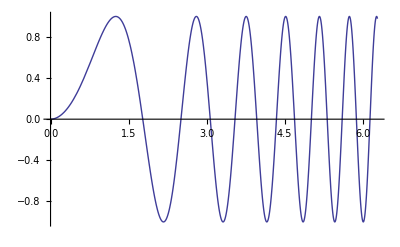

```mathematica
Plot[Sin[x^2],{x,0,2 π}]
```

... and an example of three dimensional plotting. Notice the use of options (such as PlotPoints) to control the behaviour of the function Plot3D.

```mathematica
Plot3D[Sin[π Sin[x]+y],{x,-3,3},{y,-3,3},PlotPoints->33,Axes->None,Boxed->False]
```

## A.3 Notational Conventions

### A.3.1 Built-In Names

The names of all functions, variables, options, and constants built into Mathematica start with capital letters, e.g. Integrate, Plot. If a name consists of two or more words, the first letter of each word is capitalised, e.g. PlotPoints.

Most names of objects built into Mathematica are complete words. Unlike Unix, MS-DOS, and other systems, Mathematica rarely uses abbreviations. Abbreviations are used only where they are extremely well-known. The following table contains examples of some of the abbreviations that are built into Mathematica.

Abs    gives the absolute value of a number
Cos    gives the trigonometric function cosine
D      computes the derivative
Det    calculated the determinant of a matrix
GCD    computes the greatest common divisor

There are in the order of 1000 functions built into Mathematica. The names of the functions in general indicate the function's purpose. As an example, look at the following function names.

Eigenvalues    gives a list of eigenvalues
FindRoot       searches for a numerical solution to an equation
Integrate      evaluates the integral
Timing         returns the time used in evaluating an expression

### A.3.2 Mathematical Notation

Typically Mathematica uses English words. Most people are used to referring to standard mathematical functions with symbols rather than words, i.e. symbols such as +, -, *, /, <, and > rather than the words Plus, Minus, Times, Divide, Less, and Greater. The following table contains some of the mathematical symbols supported in Mathematica (in InputForm).

+    Plus
-    Minus, Subtract
*    Times
/    Divide
^    Power
!    Factorial
<    Less
<=   LessEqual
>    Greater
>=   GreaterEqual

In mathematical notation, the product of a and c is commonly written as a c. Mathematica also understands this notation. The asterisk * denoting multiplication is optional. A blank character or space also denotes multiplication.

### A.3.3 Brackets

Be aware that Mathematica has adopted slightly different conventions from C, Pascal, and Fortran. Parentheses are used for grouping, a single set of square brackets is used for calling or specifying functions and braces are used for lists, vectors, and matrices. Here is a summary of the different types of brackets.

bracket                    Purpose                                             Examples

(term)        Grouping                  (a + b)/(c + d)
f[expr]       Arguments of function         Sin[2 Pi x]
{a,b,c}       Vectors, matrices, and lists      {x, 2 x, 3 x}
v[[i]]        Indexing                   m[[3]], m[[1,2]]
(* remark *)  Commenting                (* watch out *)

### A.3.4 Using Previous Results

Here is a result.

```mathematica
17+4
```

The percent sign (%) gives the previous result. This input multiplies the previous result by 3.

```mathematica
% 3
```

Out[n] or %n gives output n.

## A.4 Using Mathematica

### A.4.1 A next look at Graphics in Mathematica

Mathematica  has several built-in graphics functions which allow curves and surfaces to be graphed with relative ease.

First, we will do a 3-dimensional example like you might have encountered in your calculus course on functions of several variables.

```mathematica
Plot3D[(x y)/(x^2+y^2+.1),{x,-1,1},{y,-1,2}]
```

Many of Mathematica 's commands have options which can be specified. Here is a slight variation on the previous example using one of the options for Plot3D. Rather than having Mathematica  re-computing all of the points on the graph, we can use the Show[%, options] to change the display options of the previous graphic.

```mathematica
Show[%,AxesLabel->{x,y,z}]
```

Notice how the option AxesLabel effects the graph. Here is the same graph with a label.

```mathematica
Show[%,PlotLabel->"Mathematica Surface"]
```

For a complete list of the options available for Plot3D use the help browser.

Study the previous images to see how the axes are oriented by default in Plot3D.  Can you see where the first octant (the region of 3-space in which each of the variables x, y, and z is positive) is located?

Another function of 2-variables we can try is given below. Note that this example, as well as the previous one, are slightly beyond the usual graphing done by hand in a calculus course.

```mathematica
Plot3D[(x^2-y^2)^2-(x y)^2,{x,-1,1},{y,-1,1}]
```

We can modify the appearance of the above plot using some options.

```mathematica
Plot3D[(x^2-y^2)^2-(x y)^2,{x,-1,1},{y,-1,1},
	                 PlotPoints->21,
	                 BoxRatios->{1,1,.8},
			            ViewPoint->{.9,-2.4,.75}]
```

For plotting 2-dimensional graphs of a function of 1 variable, the Plot command is used.

```mathematica
Plot[x^4-4 x^3+1,{x,-1,4}]
```

Can you see the two critical points and the two inflection points in the above graph? To aid in estimating the coordinates of points, we can add options to the above plot.

```mathematica
Show[%,GridLines->Automatic,AxesLabel->{"x","y"}]
```

For another example, let's plot a curve with a skew asymptote.

```mathematica
Plot[(x^3-1)/(x^2-1),{x,-.9,5}]
```

Let's plot the asymptote in blue, and then superimpose the function and its asymptote.

```mathematica
Plot[x,{x,-1,5},PlotStyle->RGBColor[0,0,1]]
Show[%,%%]
```

By the way, notice the use of two evaluations in one cell (the Plot and Show command) and how Mathematica organises the output.

Mathematica  can also plot parametric curves in the plane. The following example is a well-known curve. Do you recognise it? Can you see the effect of the AspectRatio option?

```mathematica
ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,3 π},
		                                      AspectRatio->2/(3 π)]
```

We return to surface graphs for a final example. Many surfaces cannot be described as a graph of a function f(x,y).  A hyperboloid of 1 sheet is an example of such a surface. In order to graph these surfaces, you need to describe them using sets of parametric equations.  Once you have a surface described as a set of parametric equations in two parameters, you can use the Mathematica  function ParametricPlot3D to graph the surface. Cylindrical coordinates can be used to produce an easy parameterization of the hyperboloid described in rectangular coordinates by the equation

```mathematica
Clear[r,theta,z]
r[z_]:=√(1+z^2)
ParametricPlot3D[{r[z] Cos[theta],r[z] Sin[theta],z},
	                                           {z,-2,2},{theta,0,2 π}]
```

This example also showed how you can define your own functions in Mathematica. We will return to this point later.

### A.4.2 Algebraic Computations

Mathematica  has symbolic computing capabilities including algebra and calculus. Additionally, Mathematica can learn any computational rules you want to teach it.

Expanding and factoring polynomials can be done with

```mathematica
Expand[(9 (2+x) (x+y)+(x+y)^2)^3]
```

and

```mathematica
Factor[%]
```

Yielding a formula in a much simpler form.

Differentiation and integration are also built-in operations:

```mathematica
D[Log[x^3+Sin[x]], x]
```

```mathematica
D[(x^3+x-1)/(x^2-1), x]
```

```mathematica
Simplify[%]
```

```mathematica
∫x √(x^2+1)ⅆx
```

Of course, you can't expect Mathematica  to handle all indefinite integrals.  Can you think of an integral that Mathematica  can't evaluate? Try out your ideas.

Mathematica  also knows about power series. The next example computes the 20th degree Taylor polynomial about x=0 (sometimes called a Maclaurin polynomial) for the given function.

```mathematica
Series[(x^2-1) Sin[x^2],{x,0,20}]
```

Series can also handle purely symbolic functions such as f.

```mathematica
Series[1/2 (f[x+h]-f[x-h]) h,{h,0,6}]
```

Limit calculations are also possible symbolically. For example, Mathematica  can calculate the following limit to be e, rather than just some approximation to e .

```mathematica
Limit[(1+1/x)^x,x->∞]
```

### A.4.3 Numerical Calculations

#### A first Look

You can do arithmetic with Mathematica, just as you would on a calculator. You have seen some examples in previous chapters. However, you must realise that Mathematica can give you exact results. So, let's calculate the exact result for 3 to power 1000.

```mathematica
3^1000
```

You can use the Mathematica function N to get approximate results.

```mathematica
N[%]
```

As an exercise, find the square root of 10 to 8 digits precision (the answer is 3.1622777). Remember, the help browser answers all your questions how to do this.

Mathematica can also handle complex numbers. In Mathematica I stands for the imaginary number.

```mathematica
I^2
(3+4 I)^10
```

#### Some Mathematical Functions

The following mathematical functions are given without explanation.

N[]
Sqrt[x]
Exp[x]
Log[x]
Log[b,x]
Sin[x], Cos[x], Tan[x]
ArcSin[x], ArcCos[x], ArcTan[x]
Abs[x]
Round[x]
Mod[n, m]
Random[]
Max[x, y, ...], Min[x, y, ...]
FactorInteger[n]
RealDigits[r]
IntegerDigits[n]

The following constants are built into Mathematica .

Pi
E
Degree
I
Infinity

Here are some examples:

```mathematica
Sin[π]
```

```mathematica
Log[E]
```

```mathematica
E^(I π)
```

```mathematica
E^(-∞)
```

```mathematica
Log[2,256]
```

```mathematica
√-4
```

#### Assigning values to variables

This sets x to be 5

```mathematica
x=5
```

The x may now be used in calculations and will have the value 5.

```mathematica
x/7
```

This redefines the value for x.

```mathematica
x=2+9
```

Asking for x gives the current value of x.

```mathematica
x
```

Clear[x] or x = . clears the value for x.

```mathematica
x=.
```

The result of the input x will now be x.

```mathematica
x
```

A common source of problems in using Mathematica is trying to use variables that already have values assigned. Therefore, clear variables directly after you are finished with them or before you use them.

Because Mathematica functions begin with capital letters, you may wish to begin your own function names with lower case letters to prevent confusion.

#### Suppressing Output

Output can be suppressed by using semicolons after expressions. Semicolons can also be used to separate statements on a line.

```mathematica
x=3;y=5;z=2;
```

```mathematica
z
```

#### More Powerful Numerical Capabilities

Mathematica can evaluate all standard mathematical functions. Here is the value of the Bessel function of zeroth order of 14.5.

```mathematica
BesselJ[0,14.5]
```

You can also find approximations to roots of equations with Mathematica  using the FindRoot command. In simple cases, FindRoot uses Newton's method, so you must also specify a starting point.  FindRoot then reports the first root it encounters (there may be others).  In some cases you need to use FindRoot in conjunction with Plot to determine a good starting point.

```mathematica
Clear[x,y,z]; FindRoot[x^11-3 x^7+x-1==0,{x,2}]
```

And you can factor integers as in

```mathematica
FactorInteger[28839650461243243243243243214403592782]
```

How should the output be interpreted ?

Remember integration from section 2? Try to compute the exact value of the definite integral of 
Sin[x]^4Cos[x]^6on the interval {x, 0, 3π/4}.

Computing the required anti-derivative is somewhat involved. If you are only interested in a numerical answer, it is often faster to use a numerical routine to approximate the value of the definite integral avoiding the symbolic difficulties. This feature is illustrated next.

```mathematica
NIntegrate[Sin[x]^4 Cos[x]^6,{x,0,(3 π)/4}]
```

What about the accuracy of NIntegrate. If you have time left, try to find it experimentally, and compare with the default setting of NIntegrate?

### A.4.4 Solving Equations

Here is an algebraic equation in Mathematica

```mathematica
x^3-7 x^2+3 a x==0
```

This solves the equation on the previous line and gives the solution in terms of the parameter a.

```mathematica
Solve[%,x]
```

Here is the solution to a simple set of simultaneous equations.

```mathematica
Solve[{a x+b y==0,x+y==c},{x,y}]
```

Mathematica can also solve differential equations. Here is the closed form solution for y''(x) - ky(x) = 1.

```mathematica
DSolve[y''[x]-k y[x]==1,y[x],x]
```

Mathematica also solves equations numerically. If you would try to solve the equation x^5+2x+1=0, you would find

{{x→Root[1+2 #1+#1^5&,1]},{x→Root[1+2 #1+#1^5&,2]},{x→Root[1+2 #1+#1^5&,3]},{x→Root[1+2 #1+#1^5&,4]},{x→Root[1+2 #1+#1^5&,5]}}

which means that Mathematica could not find an explicit algebraic form, and leaves the results in a symbolic form.

Note that the syntax above is further explained in section 1.4.8

Applying N gives the numerical results

```mathematica
Solve[x^5+2 x+1==0,x]
```

```mathematica
N[%]
```

If you are only interested in numerical results, it is usually a lot faster to use the function NSolve to ask for a numerical results.

```mathematica
NSolve[x^5+2 x+1==0,x]
```

NSolve gives you a general way to find numerical approximations to the solutions of polynomial equations. Finding numerical solutions to more general equations, however, can be much more difficult. FindRoot gives you a way to search for a numerical solution to an arbitrary equation, or set of equations. Below is an example how FindRoot allows you to solve transcendental equation numerically. This gives the solution to a pair of simultaneous equations near x = 1, y = 0.

```mathematica
FindRoot[{Sin[x]==x-y,Cos[y]==x+y},{x,1},{y,0}]
```

As you would expect by now, Mathematica can also find numerical solutions to differential equations. Below, NDSolve solves for the function y with x in the range 0 to 20.

```mathematica
NDSolve[{y''[x]+Sin[x]^2 y'[x]+y[x]==Cos[x]^2,y[0]==1,y'[0]==0},y,{x,0,20}]
```

The solution is given as an interpolating function, which allows to find values of y(x) for specific values of x. Below we take the solution and plot it as a function of x.

```mathematica
Plot[Evaluate[y[x]/.%],{x,0,20}]
```

#### Intermezzo, the /. Construction, Applying Transformation Rules

When transforming an expression like x + x to 2x , Mathematica treats x in a purely symbolic manner. One way to replace x with a definite value is to apply a transformation rule.

This is how you apply a transformation rule. You can think of this as "in the expression 2x replace all x with 3."

```mathematica
2 x/.x->3
```

You can replace x with an expression.

```mathematica
1+2 x+4 x^2/.x->2-y
```

You can apply lists of rules.

```mathematica
(x+y) (x-y)/.{x->3,y->2}
```

More information on transformation rules is given in section 4.6.

### A.4.5 Lists and Matrices

#### Making Lists of Objects

Lists are a way to make collections of objects in Mathematica. Lists are important structures in Mathematica.

Here is a list of three numbers.

```mathematica
{3,5,2}
```

You can perform arithmetic operations on the whole list.

```mathematica
{3,5,2}-2
```

This takes the difference between corresponding elements in the lists. The
lists must be of equal length.

```mathematica
{3,5,2}-{6,4,7}
```

You can apply mathematical functions to whole lists.

```mathematica
Exp[%]
```

You can assign the list to a variable.

```mathematica
ll=%
```

This variable ll can be used instead of the list in subsequent calculations.

```mathematica
Log[ll]
```

#### Manipulating Elements of Lists

You can refer to parts of lists by using double brackets or Part.

This takes the first element in the list.

```mathematica
{7,2,3,2,6.4}⟦1⟧
```

Notice the use of the ⟦ ⟧ symbols in the StandardForm, which in InputForm would be just double brackets, as was explained in section A.3.3.

This extracts a list of elements.

```mathematica
{3,5,4,2}⟦{3,1,3,2,4}⟧
```

You can reset the value of elements in a list. Here is a list assigned to w.

```mathematica
w={3,5,3,4,a}
```

This resets the value of the 5th element in the list to b.

```mathematica
w⟦5⟧=b
```

```mathematica
w
```

```mathematica
w=.
```

#### Making Tables of Values

The following command makes a list of the squares of the first twenty positive integers.

```mathematica
Table[i^2,{i,1,20}]
```

Next, we plot the values in the list

```mathematica
ListPlot[%]
```

A matrix is a list of lists. The next command sets a string equal to a matrix whose (i,j)-entry equals the greatest common divisor of i and j.

```mathematica
Clear[mat1]
mat1=Table[GCD[i,j],{i,1,6},{j,1,6}]
```

You can access parts of the list using double brackets or Part.

```mathematica
mat1⟦1⟧
```

```mathematica
mat1⟦6,6⟧
```

Remember the command Table, as it is very useful for future work. If you want the list to look more like a matrix you can use the command

```mathematica
MatrixForm[mat1]
```

We can compute the determinant of the matrix with

```mathematica
Det[mat1]
```

Since the determinant is non-zero, we can calculate the inverse matrix.

```mathematica
Clear[mat2]
mat2=Inverse[mat1]
```

Finally, we can verify that the product of the matrix and its inverse is the identity matrix.

```mathematica
MatrixForm[mat1.mat2]
```

Mathematica can also manipulate symbolic matrices. This finds the eigenvectors of a matrix, then simplifies the algebraic result.

```mathematica
Simplify[Eigenvectors[{{a,b},{-b,2 a}}]]
```

Here's a list of other Mathematica functions which work with matrices and lists.

Array[a,n] or Array[a, {n,m}]
Range[n]
Length[list]
ColumnForm[list]
Dimensions[list]
MatrixForm[list]
MatrixPower[m,n]
Inverse[m]
Det[m]
Transpose[m]
Eigenvectors[m]
Eigenvalues[m]

#### Getting Parts of Lists

Here are some functions to use for taking parts of lists.

First[list]
Last[list]
Part[list,n]
Take[list,n]
Rest[list]
Drop[list,n]

#### Rearranging Lists

Some functions for rearranging lists

Sort[list]
Union[list]
Reverse[list]
RotateLeft[list,n]
RotateRight[list,n]

### A.4.6 More on Transformation Rules

You have already seen how to use a rule, for instance x → 1 + a on a algebraic expression.

```mathematica
1+x^2+3 x^3/.x->1+a
```

You can give transformation rules for any expression. Here's a rule for f[2].

```mathematica
{f[1],f[2],f[3]}/.f[2]->b
```

More general, this replace f[anything], where anything is named n, by n^2.

```mathematica
{f[1],f[2],f[3]}/.f[n_]->n^2
```

Here is a Mathematica function definition, specifying that f[n] is always to be transformed to n^2.

```mathematica
f[n_]:=n^2
```

```mathematica
f[3]+f[a+b]
```

Using the question mark gives information about the rules you have defined for a function.

```mathematica
?f
```

Actually, the question mark also provides information on build-in functions

```mathematica
?Plot3D
```

Here is a way to get extra information including Attributes and Options.

```mathematica
??Plot3D
```

You can also use wild cards.

```mathematica
?*Plot*
```

Returning to the transformation rules, you can also define recursive rules, e.g. for the factorial function.

```mathematica
fac[n_]:=n fac[n-1]
```

Also provide a rule for the end condition of the function.

```mathematica
fac[1]:=1
```

Here are once more the rules you just defined.

```mathematica
?fac
```

Mathematica  can now apply these rules to find the value for factorials.

```mathematica
fac[20]
```

Compare the result with the build-in factorial function.

### A.4.7 Using Add-On Packages

Mathematica  comes with several packages for special applications.  Packages must be loaded into a session before they can be used.

The various packages are located in the Packages sub-folder of the Mathematica folder.  Information about them can be found in the book Mathematica Standard Add-On Packages  which is part of the standard Mathematica  distribution, and also in the help browser. Also, the help browser helps in getting information on the available packages. The following example illustrates the use of a package.

```mathematica
<<"PolyhedronOperations`"
```

This command loads the package Polyhedra. Now that the package has been loaded, we can use some of the commands which are defined in the package.

```mathematica
Show[PolyhedronData["`"]]
```

### A.4.8 Programming in Mathematica

#### Examples

Mathematica  is also a high-level programming language with capabilities for iteration, looping, user-defined functions, etc.

The following code displays the graphs of a function for several different values of the parameter a.

```mathematica
Clear[f,x,a]
f[x_,a_]:=x^3+a x+1;
Do[
	     Plot[f[x,a],{x,-3,2},PlotRange->{-2,3}],
       {a,-3,2,.25}]
```

The above example involves a straightforward Do loop which generates a list of graphics. One very useful feature about such a list is that it can be animated. If you select the graphics by clicking the appropriate enclosing cell bracket, choose the Cell menu, then choose Animate Selected Graphics, an animation will begin. You can control various aspects of the animation by clicking the buttons in the lower left of the window.  Click anywhere in the middle of the window to stop the animation. If you close the cell group containing all the graphics you only see the first generated graphic. Double-clicking on the this graphic now suffices to start the animation

If you want to print an animation, of course there is a problem. You could print one frame per page to generate a kind of flip book animation. Or, you could just print several frames per page is some type of matrix arrangement.  The GraphicsArray command make the latter possible as is illustrated below.

```mathematica
Clear[f,g,glist,x,a]
f[x_,a_]:=x^3+a x+1;
g[a_]:=Plot[f[x,a],{x,-3,2},PlotRange->{-2,3},DisplayFunction->Identity];
glist=Table[g[a],{a,-3,2}];
Show[GraphicsGrid[Partition[glist,3]]]
```

You can often avoid using loops in Mathematica by operating directly on complete lists. The resulting programs are usually more elegant and more efficient. Here are programs to calculate the means and variance of a list. The pattern numlist_List only matches lists.

```mathematica
mean[numlist_List]:=Apply[Plus,numlist]/Length[numlist];
variance[numlist_List]:=mean[(numlist-mean[numlist])^2]
```

```mathematica
ll={1,2,3,4,5,6,7,8,9}
```

```mathematica
mean[ll]
```

```mathematica
variance[ll]
```

```mathematica
mean[66]
```

The final results shows the action of the pattern matching of the numlist_List construction. Mathematica does not have a rule to apply mean to an integer, and therefore returns mean[66]. You could also apply a rule for the case that you give an integer to the function mean.

```mathematica
mean[n_Integer]:=Print["Apply a list of numbers"]
```

```mathematica
mean[66]
```

Here's another example of the use of lists. We will compare the graphs of Sin[x] with those of its first eight Maclaurin polynomials. Rather than inputting the formulas for the polynomials by hand, and rather than use the Mathematica  built-in command Series, we will build a table of the polynomials all at once. This is done in a single line of input to Mathematica  (spread out over a number of lines of code below for readability).  Note that this line of input contains what would amount to a nested double Do loop in many other programming languages.

```mathematica
Clear[functionlist]
functionlist=Table[∑_(i=0)^n ((-1)^i x^(2 i+1))/((2 i+1)!),{n,0,7}];
AppendTo[functionlist,Sin[x]];
colorlist=Table[RGBColor[0,0,t],{t,.1,1,(.9)/7}];
AppendTo[colorlist,RGBColor[1,0,0]];
Plot[Evaluate[functionlist],{x,0,7},
	           PlotStyle->colorlist]
```

Finally, here is a program which plots the solutions to a polynomial equation as points in the complex plane. The /; clause at the end checks if poly is indeed a polynomial if the variable z. It fulfills the same function as the pattern matching rules introduced above. Furthermore, notice the use of the /. construction.

```mathematica
rootplot[poly_,z_]:=ListPlot[{Re[z],Im[z]}/.NSolve[poly==0,z],
		                      AspectRatio->1,
		                      AxesLabel->{Re,Im}
		                    ]/;PolynomialQ[poly,z]
```

```mathematica
rootplot[x^100+10 x+1,x]
```

And again see the result of check on poly.

```mathematica
rootplot[Sin[z]^2,z]
```

Actually, in all these examples you have seen a number of different programming paradigms which are all supported by Mathematica. In the next parts of this section these different paradigms are listed, and for each an example is presented. This overview, together with the (long) list of programming functions as you can find in the help browser gives you a good idea of the very powerful programming capabilities of Mathematica.

#### Procedural Programming

```mathematica
z=a;
Do[Print[z*=z+i],{i,3}]
```

#### List-based Programming

```mathematica
1+{a,b,c}^2
```

```mathematica
Table[i^j,{i,4},{j,4}]
```

The next line Flattens out the sublists:

```mathematica
Flatten[%]
```

The next line partitions into sublists of length 2

```mathematica
Partition[%,2]
```

List based programming is a very handy way to manipulate large amounts of information. To get a feeling of the power of this paradigm, write as, an exercise a procedural program that does the same as in the first example.

#### Functional Programming

```mathematica
NestList[f,x,4]
```

When you use functional operations such as NestList, you always have to specify a function to apply. In the example above, we have used the "name" of a function to specify the function. Pure functions allow you to give functions which can be applied to arguments, without having to define explicit names for the functions.

The red indicates a 'pure function'

```mathematica
NestList[(1+#)^2&,x,3]
```

The # indicates the first variable in a pure function; the & indicates that the preceeding part is the body of a pure function. If you want to define more variables to a pure function you can use #1, #2, etc. You can also define a pure function with Function.

```mathematica
Nest[Function[q,1/(1+q)],x,3]
```

```mathematica
Nest[1/(1+#1)&,x,3]
```

Technical note : If you are familiar with formal logic or the LISP programming language, you will recognize Mathematica pure functions as being like λ expressions or anonymous functions. Pure functions are also close to the pure mathematical notion of operators.

#### Advanced Topic: Rule-based Programming

```mathematica
p[x_+y_]:=p[x]+p[y]
```

```mathematica
p[a+b+c]
```

Notice that Mathematica repeatedly applies the rules it knows to evaluate the expression.

The red stands for any sequence of expressions

```mathematica
s[{x__,a_,y__},a_]:={a,x,x,y,y}
```

```mathematica
s[{1,2,3,4,5,6},4]
```

To clarify the use of the x__ a little bit further you should realise that the use of a parttern like f[x_,y_] stands only for instances of the function with exactly two arguments. Sometimes you need to set up patterns that can allow any number of arguments. A double blank, like x__ stands for a sequence of one or more expressions. A triple blank, like x___, stands for a sequence of zero or more expressions

Here is an example, using triple blanks, of a rule which picks out pairs of duplicated elements.

```mathematica
h[a___,x_,b___,x_,c___]:=hh[x] h[a,b,c]
```

```mathematica
h[2,3,2,4,5,3]
```

You should be very careful whenever you use triple blank patterns. It is easy to make mistakes that lead to an infinite loop (a "livelock"). If  you e.g. define p[x_, y___] := p[x] q[y], then typing p[a] will lead to an infinite loop, with y repeatedly matching a sequence with zero elements.

#### Advanced Topic: Object-oriented Programming

When you make a definition in the form f[args] = rhs or f[args] := rhs, Mathematica associates your definition with the object f. This means, for example, that such definitions are displayed when you type ?f. Mathematica however also supports upvalues, which allow definitions to be associated with symbols that do not appear directly as their head.

Consider for example a definition like Exp[g[x_]] := rhs. One possibility is that this definition could be associated with the symbol Exp, and considered as a downvalue of Exp. This is however not the best thing to do. Better is to consider Exp[g[x_]] := rhs to be associated with g, and to correspond to an upvalue of g.

This defines a downvalue for f.

```mathematica
Clear[f,g]
f[g[x_]]:=fg[x]
```

```mathematica
?f
```

This defines an upvalue for g.

```mathematica
g/:Exp[g[x_]]:=expg[x]
```

```mathematica
?g
```

Global`g

The definition is not associated with Exp.

```mathematica
?Exp
```

In simple cases, you will get the same answers to calculations whether you give a definition for f[g[x]] as a downvalue of an upvalue for g. However, one of the two choices is usually much more natural and efficient than the other. A good rule of thumb is that the definition for f[g[x]]  should be given as an upvalue for g in cases where the function f is more common than g.

Upvalues provide a convenient mechanism for specifying how operations act on objects that are tagged to have a certain type. For example, you might want to introduce a class of abstract mathematical objects of type quat. You can represent each object of this type by a Mathematica expression of the form quat[data]. In a typical case, you might want quat objects to have special properties with respect to arithmetic operations such as addition and multiplication. You can set up such properties by defining upvalues for quat with respect to Plus and Times.

This defines an upvalue for quat with respect to Plus (note the other syntax compared to the previous examples, the effect is exactly the same).

```mathematica
quat[x_]+quat[y_]^:=quat[x+y]
```

```mathematica
quat[a]+quat[b]+quat[c]
```

When you define an upvalue for quat with respect to an operation like Plus, what you are effectively doing is to extend the domain of the Plus operation to include quat objects. You are telling Mathematica to us special rules for addition in the case where the things to be added are quat objects. In defining addition for quat objects, you could always have a special addition operation, say quatPlus, to which you assign an appropriate downvalue. It is usually much more convenient, however, to use the standard Mathematica Plus operation to represent addition, but then to "overload" this operation by specifying special behaviour when quat objects are encountered.

You can think of upvalues as a way to implement certain aspects of object-oriented programming. A symbol like quat represents a particular type of object. Then the various upvalues for quat specify "methods" that define how quat objects should behave under certain operations, or on receipt of certain "messages".

#### Advanced Topic: Mixed Programming

Mathematica allows to us all different paradigms in a mixed programming style. Here are some examples. Anlyse the examples and try to distinguish between the different programming styles that are used.

```mathematica
Position[1/2 {1,2,3,4,5},_Integer]
```

```mathematica
MapIndexed[Power,{a,b,c,d}]
```

```mathematica
FixedPointList[If[EvenQ[#1],#1/2,#1]&,10^5]
```

#### Advanced Topic: The Result is Flexibility

Mathematica gives you the flexibility  to write programmes in many different styles:
What follows is 12 ways to define the factorial function:

```mathematica
f=Factorial
```

```mathematica
f[n_]:=n!
```

```mathematica
f[n_]:=Gamma[n-1]
```

```mathematica
f[n_]:=n f[n-1];f[1]=1
```

```mathematica
f[n_]:=∏_(i=1)^n i
```

```mathematica
f[n_]:=Module[{t=1},Do[t=t i,{i,n}];t]
```

```mathematica
f[n_]:=Module[{t=1,i},For[i=1,i≤n,i++,t i];t]
```

```mathematica
f[n_]:=Times@@Range[n]
```

```mathematica
f[n_]:=Fold[Times,1,Range[n]]
```

```mathematica
f[n_]:=If[n==1,1,n f[n-1]]
```

```mathematica
f[n_]:=If[#1==1,1,#1 #0[#1-1]]&
```

```mathematica
f[n_]:=Fold[#2[#1]&,1,Array[Function[t,#1 t]&,n]]
```

## A.5 Graphics in Mathematica

### A.5.1 Introduction

In this section you will further explore the capabilities of Mathematica  for graphing curves in the plane. In addition to graphing functions of a single variable like f(x), parametric curves and polar plots will also be explored.

The primary tool for plane graphing is the function Plot. The next section studies this function along with various of its options. After skill with Plot is developed, successive sections examine graphing parametric curves in the plane, using the polar coordinate system, and animating sequences of plane graphs.

Section 5 was completely reproduced from "Graphing in the Plane" by John E. Cruthirds and L. Richard Hitt
Department of Mathematics and Statistics
University of South Alabama.

### A.5.2 Using Plot

#### The Global Behaviour of Functions

Let's look at some examples using the built-in function Plot.

First, we will graph three different fourth degree polynomials with leading coefficient 1.

```mathematica
Clear[functionlist]
functionlist={x^4-6 x^2+1,x^4-x^3+2 x^2-x+4,x^4+4 x^3-2};
```

```mathematica
Plot[Evaluate[functionlist],{x,-2,2}]
```

Technical Note: The use of the Evaluate function is necessary because Plot uses non-standard evaluation of its arguments (as explained in the Mathematica  book). The problem occurs because we did not give the Plot command the list of functions explicitly, but stored the list in a variable. If you like, you can just regard this as an idiom of the Mathematica  language and not be concerned about the details.

Well, there is not much of a pattern to observe on those plots.  Let's widen the interval a little.

```mathematica
Plot[Evaluate[functionlist],{x,-5,5}]
```

Notice that more of a pattern becomes apparent.  Finally, let's make the interval very wide.

```mathematica
Plot[Evaluate[functionlist],{x,-70,70},PlotStyle->Thickness[0.0005]]
```

Now the three graphs appear essentially the same. In other words, while the local behaviour of the three given functions was quite different (differing numbers of critical points, inflection points, etc.), the global behaviour of the three functions is essentially the same. You will have a chance to explore the global behaviour of other functions in the exercises at the end of the lab.

#### The Plot Algorithm

Our goal here is to gain some insight into how the Plot function works. At a simple level, to plot a function, you can just plot a few points and connect them with lines. To do this in Mathematica , you use the graphics primitive Line applied to a list of points. The Graphics function applied to a list of graphics primitives yields a graphics object, which can be viewed with the Show command. For example,

```mathematica
Show[Graphics[{Thickness[.01],
			         Line[{{0,0},{1,1},{2,0},{3,1},{4,0}}]}]]
```

Now, let's apply this graphing capability to graph a quadratic function by sampling some of its points and connecting them with line segments.

```mathematica
Clear[curve,pointlist]
pointlist=Table[{x,x^2},{x,-2,2,0.2}];
curve=ListPlot[pointlist,Joined->True,DisplayFunction->Identity]
Show[curve,Graphics[{PointSize[0.02],Point/@pointlist}],DisplayFunction->$DisplayFunction]
```

This gives a nice smooth result. The points which were plotted have been emphasised by making them larger than the lines connecting them. Notice that using more points would not significantly improve the plot of the function.

Let's try another example. This time we will just plot the points without connecting them.

```mathematica
Clear[pointlist]
pointlist=Table[{x,Sin[E^x]},{x,0.,5.,.2}];
ListPlot[pointlist]
```

That generated a bit of a mess. Let's try using more sample points.

```mathematica
Clear[pointlist]
pointlist=Table[{x,Sin[E^x]},{x,0.,5.,.05}];
ListPlot[pointlist]
```

Now let's connect the dots and see what we have.

```mathematica
ListPlot[pointlist,Joined->True]
```

That's a little better. However, we have used way too many points on the interval [0,2], and not nearly enough points on the interval [3,5].  What we need is an algorithm which dynamically decides when to use more points to obtain a reasonably accurate rendition of the function.  Well, that's exactly what the Plot function does for us.  Let's try it.

```mathematica
g1=Plot[Sin[E^x],{x,0,5}]
```

This graph gives us a pretty good idea what our function is doing, but there is still room for improving the graph. Notice, for example, that some of the relative extrema on the graph are inaccurate. A closer inspection will show that there is even a missing cycle in the above graph out near x = 5. To get a handle on improving the graph, we need to explore some of the options to the Plot function. First, let's list them together with their default values.

```mathematica
Options[Plot]
```

Three of these options determine how many sample points are used: PlotPoints, PlotDivision, and MaxBend. The value of PlotPoints is the minimum number of points which will be used to construct the graph. In fact, Plot begins by using this number of equally spaced points to sample the function values. If any two consecutive line segments constructed from those sample points produce a "bend" greater than the value of MaxBend (measured in degrees), a subdivision on one of the subintervals will occur. This process continues until all the bends are smaller than MaxBend, or until PlotDivision subdivisions have occurred. This type of algorithm is called an adaptive algorithm . The procedure adjusts the density of sample points according to the needs of the function.

With this in mind, we can try to improve our graph by adjusting some of the options to Plot. Of course, we could always set, for example, PlotDivision->10000 and MaxBend->1, but that would generate a huge number of points and would probably take more time to finish than we were willing to wait. So the goal is to judiciously increase the number of plotted points so that the graph is substantially improved. Certainly we need to increase the value of PlotDivision to allow for more subdivisions on the subintervals when needed. However, because our graph has very low curvature (is almost a straight line) except very near its relative extrema, we should actually be able to increase the value of MaxBend without unduly effecting the accuracy of the graph.  A little trial and error shows that the following values yield a reasonable improvement on our graph.

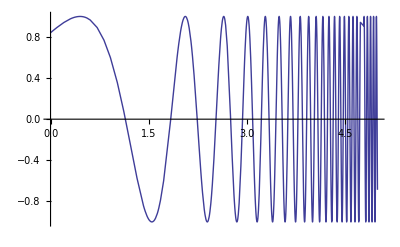

```mathematica
g2=Plot[Sin[ⅇ^x],{x,0.,5.},MaxRecursion->15,Method->{MaxBend->25}]
```

That's great. Compare the above graph with our original attempt using Plot. To aid in the comparison, you can enlarge the graph by clicking on the graph and dragging a corner to increase the size. Notice the improved uniformity on the values of the extrema and the additional cycle near the right end.

To see how many points Mathematica  plotted in the two versions of our graph requires just a bit of work. We need to know a little about the structure of the output of the Plot function in order to tell at what level the information about the actual plotted points is stored. We can get some insight into the structure of the Plot output using the following.

```mathematica
Short[InputForm[g1]]
```

If we had entered InputForm without Short, we would get the entire (very) long expression for g1. What we did get is an abbreviated form, where the <<1>> represents a single item -- a long list of points in this case. In fact, it is this list of points we want to know the length of. The <<25>> represents 25 items which have been omitted -- Plot options and their values in this case. In order to find the position of the list containing the point we can detect the level of the Line expression in g1 using

```mathematica
Position[g1,Line]
```

The result tell us that the Line command is three levels down in the expression.  So the list of ordered pairs of number is four levels down and the first point in the list is five levels down.  Thus, we try

```mathematica
Short[g1⟦1,1,1,1,1⟧]
```

which is the first point used by Plot.

We can now compute the length of the list of pairs of ordered numbers, resulting in the number of points used by Plot.

```mathematica
Length[g1⟦1,1,1,1⟧]
```

Note that the total number of points used by Plot is bounded above by the product of the two values (PlotPoints - 1) and PlotDivision. Considering the default values used by Plot, this product would be (24)(20) = 480. So Mathematica  is using close to the upper bound of points in the default graph. For the second graph, the number of points used was

```mathematica
Length[g2⟦1,1,1,1⟧]
```

So the second graph, although vastly improved over the first, did not use that many more points than the first.

Next let's look at how Mathematica  used the sample points by plotting just the points for each graph.

```mathematica
ListPlot[g1⟦1,1,1,1⟧,PlotStyle->PointSize[.01]]
```

```mathematica
ListPlot[g2⟦1,1,1,1⟧,PlotStyle->PointSize[.01]]
```

These plots illustrate how Mathematica  knows to plot points close together where the graph has high curvature but is content to spread the points out where the curvature is close to zero.

#### Advanced Topic: Functions with Asymptotes

We will examine the way Mathematica  handles functions with a vertical asymptote using an example.

```mathematica
Plot[(x^2+1)/(x-1),{x,-2,5}]
```

Note that Mathematica  appears to have drawn in the vertical asymptote. But that is not what really has happened. Remember that Mathematica  just samples values of the function at various points determined by the options PlotPoints, PlotDivision, and MaxBend, and then connects those points with straight lines.  What appears to be the asymptote is really just one of those line segments connecting a point on the left branch to a point on the right branch. The reason there is a break in the lines is that Mathematica  has truncated the graph at the top and bottom. To view all of the calculated lines, you can use the option PlotRange->All.

```mathematica
Plot[(x^2+1)/(x-1),{x,-2,5}, PlotRange -> All]
```

When you want to graph a function with a vertical asymptote,  it is usually better to split the graph along the asymptote. You can also add in the vertical asymptote separately, as well as any other asymptotes as follows.

```mathematica
Clear[g1,g2,g3]
g1=Plot[(x^2+1)/(x-1),{x,-2,.9},DisplayFunction->Identity];
g2=Plot[(x^2+1)/(x-1),{x,1.1,4},DisplayFunction->Identity];
g3=Plot[x+1,{x,-2,4},PlotStyle->{Dashing[{.02,.02}],RGBColor[1,0,0]},DisplayFunction->Identity];
Show[g1,g2,g3,Graphics[{Dashing[{.02,.02}],RGBColor[0,0,1],Line[{{1,-100},{1,100}}]}],DisplayFunction->$DisplayFunction]
```

#### Advanced Topic: Miscellaneous Options for Plot

Consider the following example.

```mathematica
Plot[x^2+1,{x,-2,2}]
```

Notice that the horizontal axis is not the x-axis, but the line y=1. Mathematica  uses its own discretion in placing the axes. If you want to override Mathematica 's decisions, you can use the PlotRange option of Plot.

```mathematica
Plot[x^2+1,{x,-2,2},PlotRange->{0,5},AxesLabel->{"x","y"}]
```

The next example illustrates several of the Plot options.

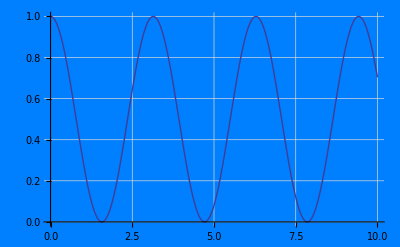

```mathematica
Plot[Cos[x]^2,{x,0,10},Background->RGBColor[0,0.5,1],GridLines->Automatic,BaseStyle->{GrayLevel[1]}]
```

### A.5.3 Advanced Topic: Parametric Plots

Curves in the plane can also be described by pairs of parametric equations of the form 
x = f(t), y = g(t). We begin by examining different ways that circles can be parameterised.

#### Parameterisations of Circles

Let's consider two different ways to graph a circle. For definiteness, let's work with the circle centred at the origin having radius 2. An equation of the circle under consideration is given by

x^2+y^2=4

To use the built-in Mathematica  function Plot to graph the above equation, we need to solve it for y:

```mathematica
Clear[x,y,solution]
solution=Solve[x^2+y^2==4,y]
```

Notice the form that Mathematica  uses to present the two solutions: it is a list of two elements, each one of which is a list containing a rule. A rule is actually a special kind of list where the first element in this case is y and the second element is the function of x. Thus we can pick out the two desired functions and graph them together with the following:

```mathematica
Clear[ytop,ybottom]
ytop=solution⟦1,1,2⟧;
ybottom=solution⟦2,1,2⟧;
Plot[{ytop,ybottom},{x,-2,2},
	           AspectRatio->Automatic]
```

Gee, that seemed like a lot of trouble just to graph a simple circle. Let's work on another approach -- a parametric approach. Recall that if you let t denote the angle made between the positive x-axis and the line from the origin to a point (x,y) on the circle, then each point on the circle is uniquely determined by the value of t, and hence, its coordinates are functions of t given by the set of equations

x(t) = 2 cos(t)
y(t) = 2 sin(t)

We can now use the built-in function ParametricPlot to graph the circle:

```mathematica
ParametricPlot[{2 Cos[t],2 Sin[t]},{t,0,2 π},AspectRatio->Automatic,AxesLabel->{x,y}]
```

Well, that was a lot easier than our first method. In the parametric equations used above, the value of the parameter t has a geometric interpretation, namely, it measures the angle indicated below.

The example above illustrates one of the main methods of obtaining a parametric set of equations for a curve  -- using an angle which is intrinsic to the curve as the parameter.

As an example of this second method, again consider the circle of radius 2 centred at the origin.  Note that any line through the point (-2,0) of the form y = t (x+2) intersects the circle in exactly one point other than (-2,0).  Thus, each point on the circle other than (-2,0) is uniquely determined by the slope t of such lines.  We can use Mathematica  to find the corresponding set of parametric equations as follows.

```mathematica
Clear[solution]
solution=Solve[{x^2+y^2==4,y==t (x+2)},{x,y}]
```

Let's graph the computed set of parametric equations and see what we get.

```mathematica
Clear[f]
f[t_]:={solution⟦2,1,2⟧,solution⟦2,2,2⟧}
ParametricPlot[Evaluate[f[t]],{t,-10,10},AspectRatio->Automatic]
```

As expected, we get the circle of radius 2 centred at the origin -- most of it, that is.  Do you see why there is a gap in the circle?  What could be done to reduce the size of the gap?

#### Lissajous Figures

A Lissajous figure is a path traced out in the plane by a particle each of whose coordinates are under simple harmonic motion. Such trajectories are often encountered in physics. The first set of parametric equations of the circle in the previous subsection is an example of such motion. Let's try some other examples which generate Lissajous figures.

```mathematica
Clear[x,y]
x[t_]:=Cos[3 t]
y[t_]:=Sin[2 t]
ParametricPlot[{x[t],y[t]},{t,0,2 π}]
```

```mathematica
Clear[x,y]
x[t_]:=Cos[3 t]
y[t_]:=Cos[4 t+π/4]
ParametricPlot[{x[t],y[t]},{t,0,2 π}]
```

### A.5.4 Advanced Topic: Polar Plots

In this section we will graph some curves in polar coordinates.  To begin with we need to recall the transformation equations from rectangular coordinates to polar coordinates.

x = r Cos[θ]
y = r Sin[θ]

So, to graph a polar equation like r = Sin[2θ], all we need do is

```mathematica
Clear[r]
r:=Sin[2 t]
ParametricPlot[r {Cos[t],Sin[t]},{t,0,2 π},
	                                     AspectRatio->Automatic]
```

Exercise: Now try to graph  r = 1 +  Cos[θ]

Exercise: Now try to graph a five petal rose.

### A.5.5 Animations

Mathematica  can perform animations of sequences of graphics. To generate such an animation, you first construct the list of graphics, often using a Do loop or similar construct.  Then you select the cell which contains the list of graphics by clicking the appropriate cell bracket.  Next, from the Cell pull down menu, you select Animate Selected Graphics.  At that point, you should begin to see an animation.  You can control various aspects of the animation by clicking on buttons on the lower left of the window.  Consult the Mathematica User's Guide for the Macintosh  for details.

The following example illustrates various limacons -- those with loops, those without loops, and cardiods. As the parameter a varies, the limacon changes in a way which can be viewed by animating the generated graphics.

```mathematica
Do[ParametricPlot[(1+a Cos[theta]) {Cos[theta],Sin[theta]},{theta,0,2 π},PlotRange->{{-4.5,4.5},{-2.5,2.5}}],{a,-3.5,3.5,.5}]
```

As you might expect, Mathematica has a number of functions to ease the task of animation.

For another animation, we can expand on the Lissajous figures introduced in the previous section. We will watch what happens as we shift the phase of the harmonic motion on the y-axis for a particular Lissajous figure. Animate the result of the following code and watch what happens.

```mathematica
x[t_]:=Cos[2 t]
y[t_,a_]:=Cos[5 (t+a)]
Animate[ParametricPlot[{x[t],y[t,a]},{t,0,2 π},AspectRatio->Automatic],{a,0,π/5-π/120,π/120}]
```

It is not completely obvious how the interval for the parameter a was selected.  The idea was to use the smallest interval which brings the graph back to where it started.

### A.5.6 Implementation

Here is the Mathematica  code that was used to generate one of the circle graphics in the Parametric Plots section.

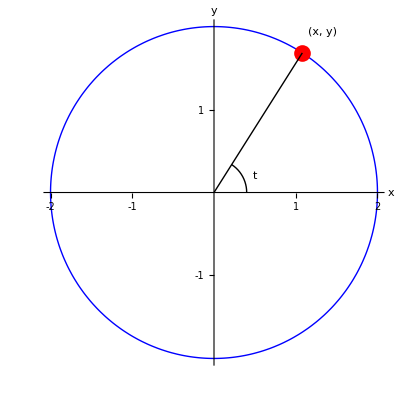

```mathematica
Clear[f,t,a]
a=1;
f[t_]={2 Cos[t],2 Sin[t]};
ellipse=ParametricPlot[f[t],{t,0,2 π},AspectRatio->Automatic,PlotStyle->RGBColor[0,0,1],DisplayFunction->Identity];
point=Graphics[{RGBColor[1,0,0],PointSize[0.03],Point[f[a]]}];
pointlabel=Graphics[Text["(x, y)",f[a]+{0.25,0.25}]];
line=Graphics[Line[{{0,0},f[a]}]];
angle=Graphics[Circle[{0,0},0.4,{0,ArcTan[(f[a]⟦2⟧)/(f[a]⟦1⟧)]}]];
anglelabel=Graphics[Text["t",{0.5,0.2}]];
Show[ellipse,point,pointlabel,line,angle,anglelabel,AxesLabel->{"x","y"},AspectRatio->Automatic,Ticks->{{-2,-1,1,2},{-1,1}},DisplayFunction->$DisplayFunction]
```

## A.6 Exercises

A notebook containing solutions to the following exercises should be "turned in" as your lab report. Each student is responsible for writing a lab report independently. Below you will find an example report to give you an idea what is should look like.

### Example Exercise and Report

Let f(x) = Sin(1/x).  Use Plot to graph this function on the interval (.01,1).  Then adjust the options of Plot to improve the graph as was done in the f(x) = Sin(e^x). Determine the actual number of points used in the default plot and in your improved plot.

#### Report

### Introduction

The function Plot uses an adaptive algorithm to plot functions as best as possible, as described in section 1.5.2 of notebook 1. The behaviour of the algorithm is controlled by three options, PlotPoints, PlotDivision, and MaxBend. Here we adjust these parameters in such a way to find an optimal plot of the function

```mathematica
Sin[1/x]
```

in the interval (0.01, 1) and we compare to the default settings of these options.

### Methods

As was shown in section 1.5.2 the following Mathematica code determines the number of points used in building a plot of a function f[x]. Note that we have set the options to their default values. Later on they will be set to other values.

```mathematica
graph=Plot[f[x],{x,0.01,1},PlotPoints->25,MaxBend->10,MaxRecursion->15]
Length[graph⟦1,1,1,1⟧]
```

The function Sin[1/x] has minima and maxima of -1 and 1 for 1/x = nπ, with n an integer. If x becomes small, the function will exhibit many of these extrema. It is expected that the Plot algorithm with its default settings will have problems in these regions, comparable with the example in section 1.5.2 of notebook 1. This is caused by a relative large value of MaxBend, in combination with a small value of PlotDivision. The Plot options will be adapted, in a trial and error process, in such a way to increase the quality of the graph. We expect that  the MaxBend and PlotDivisions options will especially have a major impact, as they control the detailed behaviour of the adaptive plotting algorithm used by Plot; MaxBend controls the further subdivision of plotting intervals and PlotDivision controls the maximum allowed number of subdivisions.

### Results

First, we plot the graph and determine the number of points for the default settings of Plot.

```mathematica
graphdefault=Plot[Sin[1/x],{x,0.01,1},PlotPoints->25,MaxBend->10,MaxRecursion->15]
Length[graphdefault⟦1,1,1,1⟧]
```

⁃Graphics⁃

153

The number of points is 153. Next we try to adapt the options in such a way that the number of points does not increase too much, but that the quality of the graph improves. In the range [0.01-0.1] the graph needs some special attention. The value of the minima and the maxima should be aligned at respectively -1 and +1. We start with increasing PlotDivision and decreasing MaxBend and PlotPoints.

```mathematica
graph1=Plot[Sin[1/x],{x,0.01,1},PlotPoints->15,MaxBend->5,MaxRecursion->15]
Length[graph1⟦1,1,1,1⟧]
```

⁃Graphics⁃

316

On first inspection this graph looks reasonably well. However, if we enlarge the region from 0.01 to 0.1 the following is observed.

```mathematica
Show[graph1, PlotRange -> {{0.01,0.1},Automatic}]
```

⁃Graphics⁃

We see that for the smallest values of x the graph is still not as expected. This can be improved by either increasing PlotPoints....

```mathematica
graph2=Plot[Sin[1/x],{x,0.01,1},PlotPoints->50,MaxBend->5,MaxRecursion->15,PlotRange->{{0.01,0.1},Automatic}]
Length[graph2⟦1,1,1,1⟧]
```

⁃Graphics⁃

578

...or better, increasing PlotDivision...

```mathematica
graph3=Plot[Sin[1/x],{x,0.01,1},PlotPoints->15,MaxBend->5,MaxRecursion->15,PlotRange->{{0.01,0.1},Automatic}]
Length[graph3⟦1,1,1,1⟧]
```

⁃Graphics⁃

618

On the full scale the last graph looks as follows.

```mathematica
Show[graph3, PlotRange -> All]
```

⁃Graphics⁃

### Discussion

The default settings of Plot results in a poor graph of Sin[1/x] in the specified range. The final results (graph2 and graph3) show a good improvement over the default graph, however, the number of points is increased from 153 to 618.

Finding optimal values for the options in a trial and error way is not straightforward, and requires some experimentation. Also, the definition of optimal depends on the range of plotting.

### Exercise 1

Find a 10-digit number which is prime.

### Exercise 2

Plot a graph of the function f(x,y)=Cos(√(x^2+y^2)) over some suitable region in the xy-plane containing the origin. Experiment with the region and possibly with the PlotPoints option of Plot3D to obtain a pleasing and informative rendering of the graph.

### Exercise 3

Let  f(x)=2 x^3-6x+3  and  g(x)=-4 x^3+3 x^2+2 .
(a)  Use the graphing capabilities of Mathematica  to graph both functions on a single set of axes.  Examine the graphs and visually estimate the number of points of intersection of the two curves as well as the coordinates of the points of intersection.
(b)  Use the symbolic capabilities of Mathematica  to find the exact values of the x and y coordinates of the points of intersection of the two curves.
(c)  Use the numerical capabilities of Mathematica  to find approximate values for the x and y  coordinates of intersection of the two curves.

### Exercise 4

Consider the function f(x)=(x^3+x+1)/(x^4+1).
(a)  Using the symbolic capabilities of Mathematica , find simplified formulas for f'(x) and for f''(x)
(b) Find all real roots of f'(x) and of f''(x). These numbers are then candidates for relative extrema and for inflection points.
(c)  Rather than applying the first or second derivative tests to classify the critical points, simply graph f(x), f'(x), and f''(x) on the same set of axes over some appropriate interval and interpret what you see. Give a full explanation of which points found in (b) above are relative extrema and which are inflection points. To keep the three graphs straight, plot them in blue, red, and green, respectively.

### Exercise 5

To gain practice and understanding of the Plot options PlotPoints, PlotDivision, and MaxBend, adjust these options so that the graph of f(x)=x^2 consists of exactly four straight line segments.

### Advanced Exercise 1

Construct a graph of the function

f(x)=(x^3+x+1)/(x^2-x-6)

as was done in the similar example. That is, split the graph along the vertical asymptotes. Also, graph the vertical asymptotes in a different color, and do the same for the skew asymptote.

### Advanced Exercise 2

(a)  Graph the ellipse given by the equation

x^2/9+y^2/4=1

using ParametricPlot.

(b)  Graph the hyperbola given by the equation

x^2/9-y^2/4=1

using ParametricPlot.

### Advanced Exercise 3

This exercise concerns a famous curve called the "folium of Descartes."  The rectangular equation for this curve is

x^3+y^3=6xy .

(a) To graph this equation, the first step might be to solve for y as a function of x.  Do this using the Solve function.  Observe that the result is a complete mess.  

(b) Rather than proceeding with the above train of thought, parameterise the curve using slopes of straight lines through the origin.  You can do this using the Solve function again, as was done in the Parameterizations of Circles subsection of the lab.  Note that the results tell you that such straight lines intersect the curve in at most one point other than the origin.

(c) Now try to graph the curve using the ParametricPlot function with an interval of [-10,10].

(d)  If all has gone correctly, you will have a plot which is not possibly correct.  It will contain curves and a straight line, and will not have the property that straight lines through the origin intersect the graph in only one point other than the origin -- a fact which is guaranteed by part (b) above.

(e)  Explain what has gone wrong, fix it, and give a correct graph of the folium of Descartes.

Partition::pdep: Depth 1 requested in object with dimensions {}.